# 利萨茹曲线

### 数学上，利萨茹（Lissajous）曲线（又称利萨茹图形、李萨如图形或鲍迪奇（Bowditch）曲线）是两个沿着互相垂直方向的正弦振动的合成的轨迹。 纳撒尼尔·鲍迪奇在1815年首先研究这一族曲线，朱尔·利萨茹在1857年作更详细研究。

利萨茹曲线由以下参数方程定义：

其中-Graphics-，-Graphics-。

```mathematica
Manipulate[ParametricPlot[{a Sin[θ],b Sin[n θ+ϕ]},{θ,0,t π},PlotRange->({-1,1}#&)/@{a+0.5,b+0.5},PlotStyle->{Thick,Magenta}],{a,1,5},{b,1,5},{ϕ,0,π/2},{n,1,10},{t,0.01,50}]
```

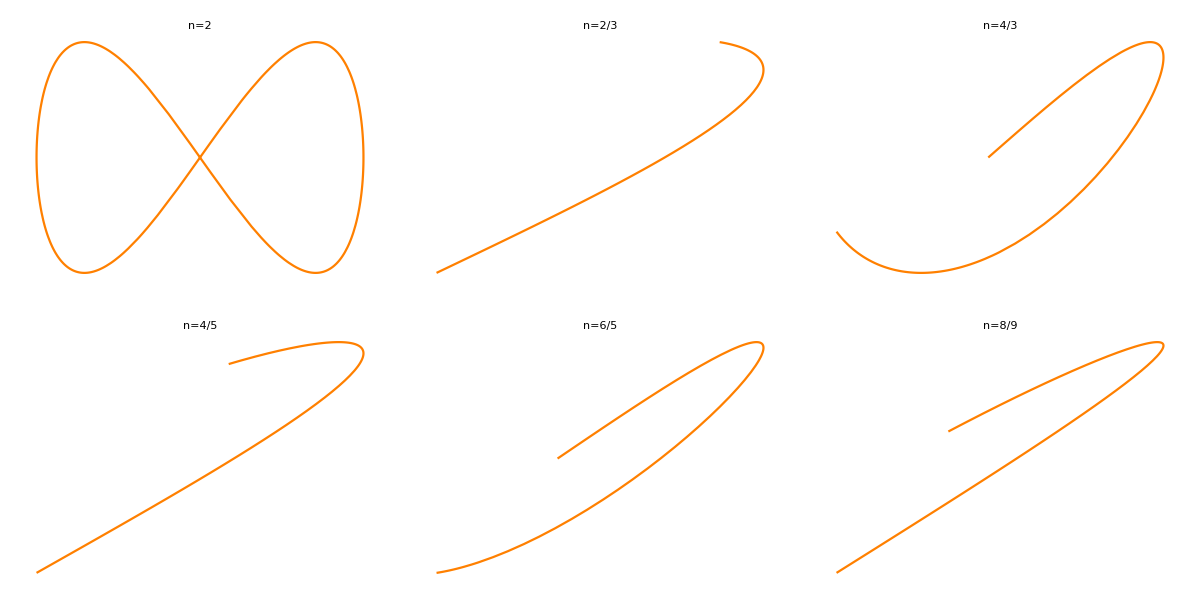

5656

```mathematica
l=Table[ParametricPlot[{Sin[θ],Sin[n θ]},{θ,0,n π},PlotStyle->{Orange},Axes->False,PlotLabel->StringForm["n=``",n]],{n,{2,2/3,4/3,4/5,6/5,8/9}}];
Grid[Partition[l,3],Frame->All,Background->GrayLevel[0.8]]
```